# Omicron analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries

```mathematica
dataset="omicron-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={"Sweden","Turkey"};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-01

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2021-12-21

```mathematica
countries=Union[seqData[[All,2]]]
```

{Australia,Brazil,Canada,Denmark,France,Germany,India,Ireland,Israel,Netherlands,Norway,Portugal,Singapore,South Africa,Spain,Sweden,Switzerland,Turkey,United Kingdom,USA}

```mathematica
countries=Complement[countries,countriesToDrop]
```

{Australia,Brazil,Canada,Denmark,France,Germany,India,Ireland,Israel,Netherlands,Norway,Portugal,Singapore,South Africa,Spain,Switzerland,United Kingdom,USA}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-15;;-1]]&,countries]
```

{Australia→{{2021-12-07,213},{2021-12-08,207},{2021-12-09,242},{2021-12-10,135},{2021-12-11,83},{2021-12-12,274},{2021-12-13,118},{2021-12-14,229},{2021-12-15,167},{2021-12-16,91},{2021-12-17,77},{2021-12-18,60},{2021-12-19,37},{2021-12-20,88},{2021-12-21,137}},Brazil→{{2021-12-07,113},{2021-12-08,109},{2021-12-09,59},{2021-12-10,15},{2021-12-11,5},{2021-12-12,5},{2021-12-13,22},{2021-12-14,47},{2021-12-15,45},{2021-12-16,28},{2021-12-17,16},{2021-12-18,11},{2021-12-19,5},{2021-12-20,0},{2021-12-21,0}},Canada→{{2021-12-07,253},{2021-12-08,211},{2021-12-09,183},{2021-12-10,81},{2021-12-11,48},{2021-12-12,22},{2021-12-13,19},{2021-12-14,26},{2021-12-15,8},{2021-12-16,10},{2021-12-17,0},{2021-12-18,0},{2021-12-19,0},{2021-12-20,0},{2021-12-21,0}},Denmark→{{2021-12-07,1909},{2021-12-08,1647},{2021-12-09,1148},{2021-12-10,1604},{2021-12-11,1127},{2021-12-12,890},{2021-12-13,975},{2021-12-14,686},{2021-12-15,604},{2021-12-16,472},{2021-12-17,61},{2021-12-18,315},{2021-12-19,529},{2021-12-20,170},{2021-12-21,168}},France→{{2021-12-07,364},{2021-12-08,214},{2021-12-09,206},{2021-12-10,188},{2021-12-11,152},{2021-12-12,79},{2021-12-13,756},{2021-12-14,123},{2021-12-15,104},{2021-12-16,67},{2021-12-17,35},{2021-12-18,18},{2021-12-19,22},{2021-12-20,0},{2021-12-21,0}},Germany→{{2021-12-07,1078},{2021-12-08,430},{2021-12-09,1351},{2021-12-10,766},{2021-12-11,330},{2021-12-12,50},{2021-12-13,50},{2021-12-14,87},{2021-12-15,107},{2021-12-16,137},{2021-12-17,16},{2021-12-18,5},{2021-12-19,3},{2021-12-20,0},{2021-12-21,0}},India→{{2021-12-07,82},{2021-12-08,75},{2021-12-09,64},{2021-12-10,29},{2021-12-11,21},{2021-12-12,46},{2021-12-13,37},{2021-12-14,28},{2021-12-15,29},{2021-12-16,21},{2021-12-17,22},{2021-12-18,11},{2021-12-19,9},{2021-12-20,0},{2021-12-21,0}},Ireland→{{2021-12-07,19},{2021-12-08,2},{2021-12-09,0},{2021-12-10,6},{2021-12-11,53},{2021-12-12,49},{2021-12-13,4},{2021-12-14,0},{2021-12-15,0},{2021-12-16,0},{2021-12-17,0},{2021-12-18,0},{2021-12-19,0},{2021-12-20,0},{2021-12-21,0}},Israel→{{2021-12-07,256},{2021-12-08,215},{2021-12-09,210},{2021-12-10,108},{2021-12-11,187},{2021-12-12,250},{2021-12-13,287},{2021-12-14,401},{2021-12-15,408},{2021-12-16,313},{2021-12-17,268},{2021-12-18,62},{2021-12-19,95},{2021-12-20,0},{2021-12-21,0}},Netherlands→{{2021-12-07,189},{2021-12-08,183},{2021-12-09,204},{2021-12-10,124},{2021-12-11,90},{2021-12-12,166},{2021-12-13,86},{2021-12-14,70},{2021-12-15,63},{2021-12-16,94},{2021-12-17,57},{2021-12-18,28},{2021-12-19,75},{2021-12-20,0},{2021-12-21,0}},Norway→{{2021-12-07,65},{2021-12-08,46},{2021-12-09,47},{2021-12-10,50},{2021-12-11,17},{2021-12-12,20},{2021-12-13,54},{2021-12-14,13},{2021-12-15,0},{2021-12-16,0},{2021-12-17,0},{2021-12-18,0},{2021-12-19,0},{2021-12-20,0},{2021-12-21,0}},Portugal→{{2021-12-07,36},{2021-12-08,73},{2021-12-09,15},{2021-12-10,12},{2021-12-11,32},{2021-12-12,104},{2021-12-13,154},{2021-12-14,187},{2021-12-15,0},{2021-12-16,1},{2021-12-17,0},{2021-12-18,0},{2021-12-19,0},{2021-12-20,0},{2021-12-21,0}},Singapore→{{2021-12-07,37},{2021-12-08,49},{2021-12-09,29},{2021-12-10,31},{2021-12-11,32},{2021-12-12,26},{2021-12-13,21},{2021-12-14,58},{2021-12-15,60},{2021-12-16,33},{2021-12-17,45},{2021-12-18,53},{2021-12-19,59},{2021-12-20,0},{2021-12-21,0}},South Africa→{{2021-12-07,43},{2021-12-08,20},{2021-12-09,44},{2021-12-10,50},{2021-12-11,21},{2021-12-12,5},{2021-12-13,6},{2021-12-14,4},{2021-12-15,15},{2021-12-16,3},{2021-12-17,16},{2021-12-18,2},{2021-12-19,7},{2021-12-20,0},{2021-12-21,0}},Spain→{{2021-12-07,170},{2021-12-08,116},{2021-12-09,118},{2021-12-10,198},{2021-12-11,120},{2021-12-12,109},{2021-12-13,66},{2021-12-14,241},{2021-12-15,158},{2021-12-16,31},{2021-12-17,226},{2021-12-18,35},{2021-12-19,27},{2021-12-20,0},{2021-12-21,0}},Switzerland→{{2021-12-07,270},{2021-12-08,153},{2021-12-09,176},{2021-12-10,157},{2021-12-11,174},{2021-12-12,151},{2021-12-13,272},{2021-12-14,286},{2021-12-15,159},{2021-12-16,105},{2021-12-17,57},{2021-12-18,73},{2021-12-19,57},{2021-12-20,0},{2021-12-21,0}},United Kingdom→{{2021-12-07,12153},{2021-12-08,9081},{2021-12-09,7671},{2021-12-10,7488},{2021-12-11,6309},{2021-12-12,7726},{2021-12-13,9164},{2021-12-14,8641},{2021-12-15,10033},{2021-12-16,6184},{2021-12-17,4544},{2021-12-18,6351},{2021-12-19,4264},{2021-12-20,2093},{2021-12-21,264}},USA→{{2021-12-07,6943},{2021-12-08,7484},{2021-12-09,5880},{2021-12-10,5672},{2021-12-11,3283},{2021-12-12,2289},{2021-12-13,4937},{2021-12-14,6455},{2021-12-15,5713},{2021-12-16,3347},{2021-12-17,2858},{2021-12-18,1903},{2021-12-19,588},{2021-12-20,0},{2021-12-21,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountries=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
legendsForCountries=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForCountries];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

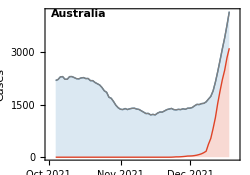
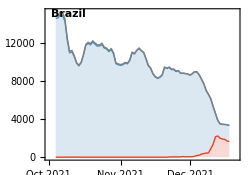
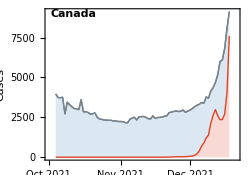
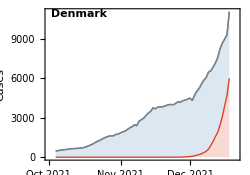
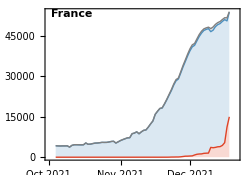
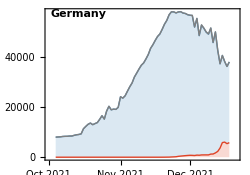
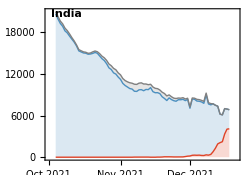
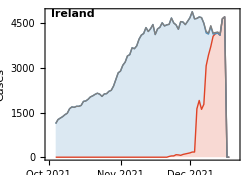
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=30000;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{8,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{8,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{8,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.88,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForCountries=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,countries];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{countries,legendsForCountries}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-log-cases.png

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/omicron-countries_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2021-12-29

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.001];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;3]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryRtPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

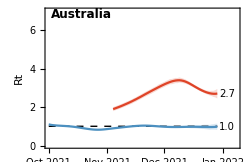
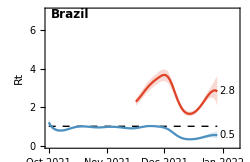
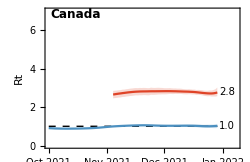
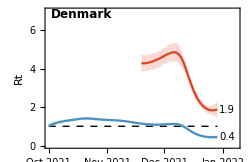
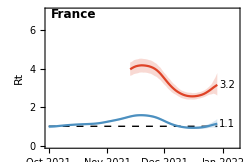
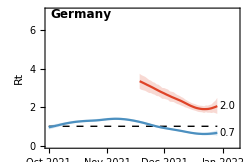
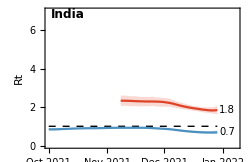
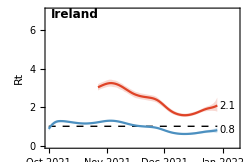
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron"][[-1,1]],Round[rtGather[#,"Omicron"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron"][[-1,2]],0.1]}&,countries]
```

{Australia→{2021-12-29,2.7,2.4,2.9},Brazil→{2021-12-29,2.8,2.1,3.6},Canada→{2021-12-29,2.8,2.6,3.},Denmark→{2021-12-29,1.9,1.4,2.3},France→{2021-12-29,3.2,2.6,3.8},Germany→{2021-12-29,2.,1.6,2.5},India→{2021-12-29,1.8,1.6,2.},Ireland→{2021-12-29,2.1,1.8,2.5},Israel→{2021-12-29,2.7,2.2,3.2},Netherlands→{2021-12-29,1.6,1.4,1.7},Norway→{2021-12-29,0.6,0.3,0.8},Portugal→{2021-12-29,3.2,2.8,3.5},Singapore→{2021-12-29,1.3,1.2,1.5},South Africa→{2021-12-29,0.5,0.3,0.6},Spain→{2021-12-29,2.4,1.9,3.},Switzerland→{2021-12-29,2.,1.5,2.4},United Kingdom→{2021-12-29,1.9,1.4,2.4},USA→{2021-12-29,2.1,1.4,2.7}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/omicron-countries_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.001];
```

```mathematica
rData=DeleteCases[rData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.35}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,14]},
{-0.35,0.35}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;3]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryLittleRPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

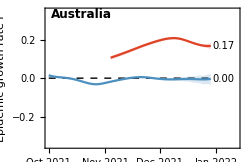
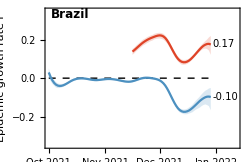
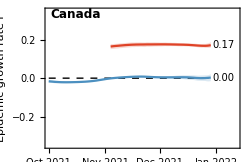
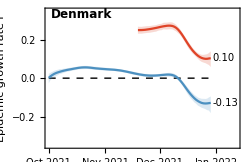
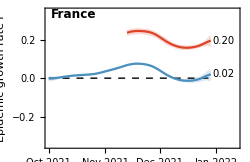
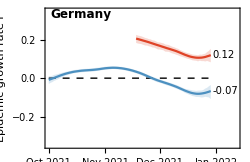
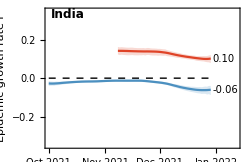
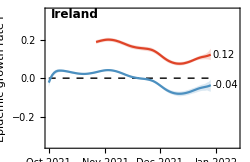
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[rGather[#,"Omicron"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,countries]
```

{Australia→{2021-12-29,0.17,0.15,0.18},Brazil→{2021-12-29,0.17,0.12,0.22},Canada→{2021-12-29,0.17,0.16,0.19},Denmark→{2021-12-29,0.1,0.06,0.14},France→{2021-12-29,0.2,0.16,0.23},Germany→{2021-12-29,0.12,0.08,0.15},India→{2021-12-29,0.1,0.08,0.12},Ireland→{2021-12-29,0.12,0.09,0.15},Israel→{2021-12-29,0.17,0.14,0.2},Netherlands→{2021-12-29,0.08,0.06,0.09},Norway→{2021-12-29,-0.08,-0.18,-0.03},Portugal→{2021-12-29,0.2,0.18,0.21},Singapore→{2021-12-29,0.05,0.03,0.07},South Africa→{2021-12-29,-0.12,-0.19,-0.07},Spain→{2021-12-29,0.15,0.11,0.18},Switzerland→{2021-12-29,0.12,0.07,0.15},United Kingdom→{2021-12-29,0.11,0.05,0.14},USA→{2021-12-29,0.13,0.06,0.17}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[Log[2]/rGather[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron"][[-1,2]],0.1]}&,countries]
```

{Australia→{2021-12-29,4.1,3.8,4.6},Brazil→{2021-12-29,4.,3.2,5.7},Canada→{2021-12-29,4.,3.7,4.4},Denmark→{2021-12-29,6.7,5.,11.9},France→{2021-12-29,3.6,3.1,4.3},Germany→{2021-12-29,5.8,4.5,8.4},India→{2021-12-29,6.8,5.8,8.8},Ireland→{2021-12-29,5.7,4.5,7.4},Israel→{2021-12-29,4.2,3.5,5.1},Netherlands→{2021-12-29,9.1,7.5,11.9},Norway→{2021-12-29,-8.2,-26.3,-3.8},Portugal→{2021-12-29,3.5,3.2,3.9},Singapore→{2021-12-29,14.2,10.1,25.8},South Africa→{2021-12-29,-5.8,-9.9,-3.7},Spain→{2021-12-29,4.6,3.8,6.6},Switzerland→{2021-12-29,6.,4.7,9.9},United Kingdom→{2021-12-29,6.4,4.8,13.6},USA→{2021-12-29,5.5,4.1,11.4}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/omicron-countries_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{8,390000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

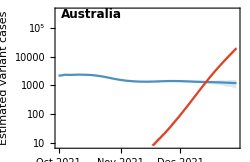
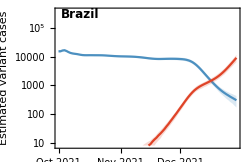
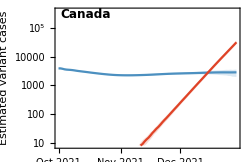
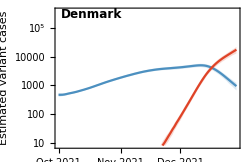
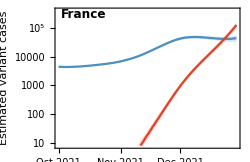
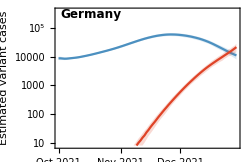
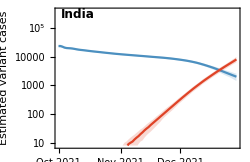
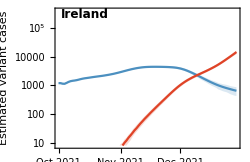
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

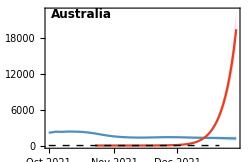
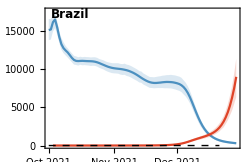
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron"][[-1,1]],Round[pGather[#,"Omicron"][[-1,2]]],Round[pGatherLower[#,"Omicron"][[-1,2]]],Round[pGatherUpper[#,"Omicron"][[-1,2]]]}&,countries]
```

{Australia→{2021-12-29,19495,16382,22590},Brazil→{2021-12-29,9020,6352,11390},Canada→{2021-12-29,31285,27119,35960},Denmark→{2021-12-29,17335,12752,21464},France→{2021-12-29,124266,99872,155904},Germany→{2021-12-29,21237,14746,27535},India→{2021-12-29,7936,6290,9605},Ireland→{2021-12-29,14307,12048,16075},Israel→{2021-12-29,2884,2370,3348},Netherlands→{2021-12-29,8708,6783,10680},Norway→{2021-12-29,554,174,934},Portugal→{2021-12-29,17134,12900,21933},Singapore→{2021-12-29,315,234,389},South Africa→{2021-12-29,6026,4729,7552},Spain→{2021-12-29,91926,59457,120053},Switzerland→{2021-12-29,11875,7775,15711},United Kingdom→{2021-12-29,180528,108189,242152},USA→{2021-12-29,317141,225426,399366}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[country_,variant_]:=Module[{popSize},
popSize=QuantityMagnitude[CountryData[country,"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[country,variant]]
]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsDelta,pairsOmicron},
pairsDelta=phaseGather[country,"Delta"];
pairsOmicron=phaseGather[country,"Omicron"];
ListLogLinearPlot[{pairsDelta,{Last[pairsDelta]},pairsOmicron,{Last[pairsOmicron]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{1,150},
{-0.25,0.4}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[2]],colors[[2]],colors[[3]],colors[[3]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-cases-vs-rt.png

```mathematica
countryLines=Map[With[{pairs=phaseGather[#,"Omicron"]},pairs]&,countries];
```

```mathematica
figLines=ListLogLinearPlot[countryLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{1,150},
{-0.1,0.35}},PlotStyle->Directive[colors[[3]],Opacity[0.5]]];
```

```mathematica
countryPoints=Map[With[{pairs=phaseGather[#,"Omicron"]},Last[pairs]]&,countries];
```

```mathematica
figPoints=ListLogLinearPlot[countryPoints,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{{1,150},
{-0.1,0.35}},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]}];
```

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

```mathematica
countryLines=Map[With[{pairs=phaseGather[#,"Delta"]},pairs]&,countries];
```

```mathematica
figLines=ListLogLinearPlot[countryLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{1,150},
{-0.1,0.35}},PlotStyle->Directive[colors[[2]],Opacity[0.5]]];
```

```mathematica
countryPoints=Map[With[{pairs=phaseGather[#,"Delta"]},Last[pairs]]&,countries];
```

```mathematica
figPoints=ListLogLinearPlot[countryPoints,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{{1,150},
{-0.1,0.35}},PlotStyle->Directive[colors[[2]]],PlotMarkers->{"•",Scaled[0.1]}];
```

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

## Comparison to vaccination rate

Country-level vaccination data is obtained from Our World in Data, following instructions at https://github.com/owid/covid-19-data/blob/master/public/data/README.md

The full CSV is available at: https://covid.ourworldindata.org/data/owid-covid-data.csv

```mathematica
comparisonDate=endDate
```

2021-12-21

### Data

```mathematica
vData=Import["https://covid.ourworldindata.org/data/owid-covid-data.csv","CSV"];
```

```mathematica
Dimensions[vData]
```

{151549,67}

```mathematica
header=First[vData]
```

{iso_code,continent,location,date,total_cases,new_cases,new_cases_smoothed,total_deaths,new_deaths,new_deaths_smoothed,total_cases_per_million,new_cases_per_million,new_cases_smoothed_per_million,total_deaths_per_million,new_deaths_per_million,new_deaths_smoothed_per_million,reproduction_rate,icu_patients,icu_patients_per_million,hosp_patients,hosp_patients_per_million,weekly_icu_admissions,weekly_icu_admissions_per_million,weekly_hosp_admissions,weekly_hosp_admissions_per_million,new_tests,total_tests,total_tests_per_thousand,new_tests_per_thousand,new_tests_smoothed,new_tests_smoothed_per_thousand,positive_rate,tests_per_case,tests_units,total_vaccinations,people_vaccinated,people_fully_vaccinated,total_boosters,new_vaccinations,new_vaccinations_smoothed,total_vaccinations_per_hundred,people_vaccinated_per_hundred,people_fully_vaccinated_per_hundred,total_boosters_per_hundred,new_vaccinations_smoothed_per_million,new_people_vaccinated_smoothed,new_people_vaccinated_smoothed_per_hundred,stringency_index,population,population_density,median_age,aged_65_older,aged_70_older,gdp_per_capita,extreme_poverty,cardiovasc_death_rate,diabetes_prevalence,female_smokers,male_smokers,handwashing_facilities,hospital_beds_per_thousand,life_expectancy,human_development_index,excess_mortality_cumulative_absolute,excess_mortality_cumulative,excess_mortality,excess_mortality_cumulative_per_million}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{iso_code→1,continent→2,location→3,date→4,total_cases→5,new_cases→6,new_cases_smoothed→7,total_deaths→8,new_deaths→9,new_deaths_smoothed→10,total_cases_per_million→11,new_cases_per_million→12,new_cases_smoothed_per_million→13,total_deaths_per_million→14,new_deaths_per_million→15,new_deaths_smoothed_per_million→16,reproduction_rate→17,icu_patients→18,icu_patients_per_million→19,hosp_patients→20,hosp_patients_per_million→21,weekly_icu_admissions→22,weekly_icu_admissions_per_million→23,weekly_hosp_admissions→24,weekly_hosp_admissions_per_million→25,new_tests→26,total_tests→27,total_tests_per_thousand→28,new_tests_per_thousand→29,new_tests_smoothed→30,new_tests_smoothed_per_thousand→31,positive_rate→32,tests_per_case→33,tests_units→34,total_vaccinations→35,people_vaccinated→36,people_fully_vaccinated→37,total_boosters→38,new_vaccinations→39,new_vaccinations_smoothed→40,total_vaccinations_per_hundred→41,people_vaccinated_per_hundred→42,people_fully_vaccinated_per_hundred→43,total_boosters_per_hundred→44,new_vaccinations_smoothed_per_million→45,new_people_vaccinated_smoothed→46,new_people_vaccinated_smoothed_per_hundred→47,stringency_index→48,population→49,population_density→50,median_age→51,aged_65_older→52,aged_70_older→53,gdp_per_capita→54,extreme_poverty→55,cardiovasc_death_rate→56,diabetes_prevalence→57,female_smokers→58,male_smokers→59,handwashing_facilities→60,hospital_beds_per_thousand→61,life_expectancy→62,human_development_index→63,excess_mortality_cumulative_absolute→64,excess_mortality_cumulative→65,excess_mortality→66,excess_mortality_cumulative_per_million→67}

```mathematica
vData=Drop[vData,1];
```

```mathematica
Length[vData]
```

151548

Replace “United States” with “USA”

```mathematica
vData=Map[Join[#[[1;;2]],{If[#[[3]]=="United States","USA",#[[3]]]},#[[4;;-1]]]&,vData];
```

Remove lines lacking data

```mathematica
vData=DeleteCases[vData,x_/;x[[43]]==""];
```

```mathematica
vData=DeleteCases[vData,x_/;x[[44]]==""];
```

```mathematica
fullyVacGather[country_]:=Module[{series},
series=Cases[vData,x_/;x[[3]]==country&&x[[4]]==comparisonDate];
If[Length[series]>0,series[[1,43]],Null]
]
```

```mathematica
fullyVacGather["United Kingdom"]
```

69.14

```mathematica
fullyVacGather["Netherlands"]
```

```mathematica
boosterGather[country_]:=Module[{series},
series=Cases[vData,x_/;x[[3]]==country&&x[[4]]==comparisonDate];
If[Length[series]>0,series[[1,44]],Null]
]
```

```mathematica
boosterGather["United Kingdom"]
```

45.22

```mathematica
totalCasesGather[country_]:=Module[{series},
series=Cases[vData,x_/;x[[3]]==country&&x[[4]]==comparisonDate];
If[Length[series]>0,100*series[[1,11]]/1000000,Null]
]
```

```mathematica
totalCasesGather["USA"]
```

15.4131

```mathematica
series=DeleteCases[Table[{country,fullyVacGather[country],boosterGather[country],totalCasesGather[country],FirstCase[rGather[country,"Omicron"],x_/;x[[1]]==comparisonDate][[2]]},{country,countries}],x_/;x[[2]]==Null||x[[3]]==Null||x[[4]]==Null]
```

{{Australia,76.08,6.47,1.02646,0.177639},{Brazil,66.32,11.11,10.3853,0.12907},{Canada,77.01,13.03,5.03871,0.170093},{Denmark,77.89,39.26,11.1457,0.124075},{France,72.45,28.34,12.9634,0.164152},{Germany,69.97,33.93,8.22336,0.106505},{Ireland,76.85,35.96,13.3789,0.0998449},{Israel,63.,44.91,14.6159,0.172625},{Norway,71.54,25.53,6.57315,-0.0716625},{Portugal,89.16,24.63,12.1323,0.184476},{Spain,80.9,25.25,11.9479,0.159016},{Switzerland,66.6,19.83,13.8188,0.0976068},{United Kingdom,69.14,45.22,16.9553,0.107297},{USA,61.26,19.61,15.4131,0.137412}}

```mathematica
fig=ListPlot[Map[{#}&,series[[All,{2,5}]]],PlotLabels->Placed[series[[All,1]],Right],PlotStyle->colors[[2]],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated fraction","Epidemic growth rate r"},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[i]<>"%"},{i,0,100,5}],Automatic}},PlotRangePadding->{{Scaled[0.02],Scaled[0.18]},{Scaled[0.03],Scaled[0.05]}},AspectRatio->0.65,Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[series[[All,2]],series[[All,5]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

```mathematica
Export["figures/"<>dataset<>"_r-vs-vaccinated-fraction.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_r-vs-vaccinated-fraction.png

```mathematica
fig=ListPlot[Map[{#}&,series[[All,{3,5}]]],PlotLabels->Placed[series[[All,1]],Right],PlotStyle->colors[[2]],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Boosted fraction","Epidemic growth rate r"},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[i]<>"%"},{i,0,100,5}],Automatic}},PlotRangePadding->{{Scaled[0.02],Scaled[0.18]},{Scaled[0.03],Scaled[0.05]}},AspectRatio->0.65,Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[series[[All,3]],series[[All,5]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

```mathematica
Export["figures/"<>dataset<>"_r-vs-boosted-fraction.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_r-vs-boosted-fraction.png

```mathematica
fig=ListPlot[Map[{#}&,series[[All,{4,5}]]],PlotLabels->Placed[series[[All,1]],Right],PlotStyle->colors[[2]],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Cumulative cases fraction","Epidemic growth rate r"},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[i]<>"%"},{i,0,100,5}],Automatic}},PlotRangePadding->{{Scaled[0.02],Scaled[0.18]},{Scaled[0.03],Scaled[0.05]}},AspectRatio->0.65,Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[series[[All,4]],series[[All,5]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

```mathematica
Export["figures/"<>dataset<>"_r-vs-infected-fraction.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_r-vs-infected-fraction.png